```mathematica
(*Problem:x''[t]+w^2x[t]==0,using laplace transform.Teh initial conditions are x[0]=1,x'[0]=0*)
deq=x''[t]+w^2*x[t]==0;
initial={x[0]->1,x'[0]->0};
?LaplaceTransform
```

LaplaceTransform[expr,t,s] gives the Laplace transform of expr. 
LaplaceTransform[expr,{t_1,t_2,…},{s_1,s_2,…}] gives the multidimensional Laplace transform of expr.

```mathematica
aeq=LaplaceTransform[deq,t,s]/.initial
```

-s+s^2 LaplaceTransform[x[t],t,s]+w^2 LaplaceTransform[x[t],t,s]==0

```mathematica
fs=Solve[aeq,LaplaceTransform[x[t],t,s]]
```

{{LaplaceTransform[x[t],t,s]→s/(s^2+w^2)}}

```mathematica
fs=LaplaceTransform[x[t],t,s]/.fs[[1]]/.w->1
```

s/(1+s^2)

```mathematica
?InverseLaplaceTransform
```

InverseLaplaceTransform[expr,s,t] gives the inverse Laplace transform of expr. 
InverseLaplaceTransform[expr,{s_1,s_2,…},{t_1,t_2,…}] gives the multidimensional inverse Laplace transform of expr.

```mathematica
xt=InverseLaplaceTransform[fs,s,t]
```

Cos[t]

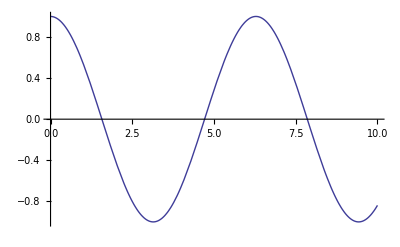

```mathematica
Plot[xt,{t,0,10}]
```